```mathematica
(*local="/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/model_driven_theory/2019"
SetDirectory[local]
incr1=-{1,3,6,9}
dayst={1,3,7,14(*6,9,12,14,18*)}
dayst={1,2,3,4(*6,9,12,14,18*)}
sigma=0.06 (*0.01,0.03,0.06*)
rg=dayst(*,10}*);
rg=Range[0,25];
filename=Flatten[Table[
{(*"cellcycletheory-sc-"<>ToString[#]<>"-rp1--5-52.-11111-1-5-5-5-0-1-"<>ToString[incr]*)
(*"cellcycletheory-sc-"<>ToString[#]<>"-rp1--5-42.-1111-1-5-5-5-0-1-"<>ToString[incr]*)
"cellcycletheory-sc-"<>ToString[#]<>"-rp1-"<>ToString[sigma]<>"-52.-11111-"<>If[incr<0,"2","0.5"]<>"-5-5-5-0-1-"<>ToString[incr]
}&/@rg,
{incr,incr1}]];
ccd1=ReadList[local<>"/data3D/"<>#<>"-0-0-0-0.5-5-2-2-1-2--1--2-0.01-0.01-0.3--1-0.dat"]&/@filename;
ccd=ccd1[[All,All,4]];*)
```

```mathematica
(*diversity2={Mean[#[[All,4]]],Length[Union[#[[All,8;;All]]]]}&/@ccd1*)
```

```mathematica
ccdList={-2,1,1.25,1.5,1.75,2.5,6}
ccdList={-2,1,1.25,1.5,1.75,2.5,6}
cL[x_,ccdList_]:=Flatten[If[(#[[1]]≤x)&&(x<#[[2]]),Position[Partition[ccdList,2,1],#],{}]&/@Partition[ccdList,2,1]]
cL[#,ccdList]&/@ccdList

coloB=Table[Blend[{ColorData["ThermometerColors"][0.15],Lighter[Pink,0.75]},i],{i,0,1.15,0.2}]
col[x_]:=Reverse[coloB][[x]]
```

{-2,1,1.25,1.5,1.75,2.5,6}

{-2,1,1.25,1.5,1.75,2.5,6}

{{1},{2},{3},{4},{5},{6},{}}

{RGBColor[0.3536047, 0.46289399999999997, 0.9223703],RGBColor[0.48288376, 0.5453152, 0.91289624],RGBColor[0.61216282, 0.6277364, 0.90342218],RGBColor[0.74144188, 0.7101576, 0.89394812],RGBColor[0.87072094, 0.7925788, 0.88447406],RGBColor[1., 0.875, 0.875]}

```mathematica
(*pos=.
bc=fc=dc=Tuples[{{}},Length[ccd]-1][[1]]
Table[
fc[[i]]=SplitBy[(Sort[{cL[#,ccdList][[1]],#}&/@ccd[[i]]]/."NA"->0),First];
,{i,1,Length[ccd]}];
fc
Table[bc[[i]]={0,0,0,0,0,0};((bc[[i]][[Mean[#[[All,1]]]]]=Length[#])&/@fc[[i]]);
(*bc[[i]]=N[bc[[i]]/Total[bc[[i]]]];*),{i,1,Length[fc]}];*)
```

```mathematica
diversity2={{2,1},{1.9401452505562586,48},{1.8790565983811662,48},{1.849267833149174,48},{1.8035125052531644,48},{1.7731638735987667,48},{1.765004697073874,48},{1.7588083311700908,48},{1.7271022528958495,48},{1.701640321735139,48},{1.6878837974335292,48},{1.6764261215912246,48},{1.6710576706010685,48},{1.666608096471897,48},{1.6675921563714504,48},{1.6685839377968628,48},{1.648096639002668,48},{1.6296077682625254,48},{1.6171522257401214,48},{1.6057450022085804,48},{1.5973909301435025,48},{1.5898716785321592,48},{1.5851191384406318,48},{1.5808044844443763,48},{1.5774505019174319,48},{1.5744147725978594,48},{2,1},{1.8202823420662821,48},{1.6400017347776599,24},{1.549858840213672,24},{1.4235669958853392,24},{1.3389209416689645,24},{1.3047867446093202,16},{1.279697179157019,16},{1.198681953621201,16},{1.1338416915866847,16},{1.0948741729241862,16},{1.0618504420521837,16},{1.0312416205444854,16},{1.0050265898697852,16},{0.9848090305373078,16},{0.9675497909040436,16},{0.9284303005083794,16},{0.8941211894994895,16},{0.8605597718889079,16},{0.8321195662899112,16},{0.8007562563594733,16},{0.7735434732921184,16},{0.7467625193340992,16},{0.7229242576706254,16},{0.6983832500357477,16},{0.6763816273471644,16},{2,1},{1.6403280368492434,48},{1.2811125831406214,16},{1.1012181585938898,16},{0.8490480604187521,16},{0.6818731298582991,16},{0.5559641513243812,16},{0.49209198012374955,16},{0.422793886470963,16},{0.379772525141436,16},{0.3452469475301261,16},{0.3164763685692822,16},{0.2921320325254913,16},{0.2712654587736705,16},{0.2531810948554258,16},{0.2373572764269617,16},{0.22339508369596395,16},{0.21098424571285485,16},{0.19987981172796773,16},{0.18988582114156935,16},{0.180843639182447,16},{0.17262347376506304,16},{0.1651181053404951,16},{0.15823818428464112,16},{0.15190865691325547,16},{0.14606601626274565,16},{2,1},{1.4604198244452056,48},{0.9201639996990016,8},{0.6514001489306154,8},{0.37100385559002047,8},{0.3086294423976517,8},{0.26453952205513004,8},{0.23147208179823878,8},{0.20575296159843445,8},{0.18517766543859102,8},{0.16834333221690093,8},{0.15431472119882586,8},{0.1424443580296854,8},{0.13226976102756502,8},{0.12345177695906068,8},{0.11573604089911939,8},{0.10892803849328883,8},{0.10287648079921723,8},{0.0974619291782058,8},{0.09258883271929551,8},{0.08817984068504334,8},{0.08417166610845046,8},{0.08051202845156132,8},{0.07715736059941293,8},{0.0740710661754364,8},{0.0712221790148427,8}};
(*diversity=Flatten[(Transpose[#]&/@Partition[diversity2,26]),1][[{2,4,6,8}]]*)
diversity1=Flatten[(Transpose[#]&/@Partition[diversity2,26]),1][[{1,3,5,7}]]
```

{{2,1.94015,1.87906,1.84927,1.80351,1.77316,1.765,1.75881,1.7271,1.70164,1.68788,1.67643,1.67106,1.66661,1.66759,1.66858,1.6481,1.62961,1.61715,1.60575,1.59739,1.58987,1.58512,1.5808,1.57745,1.57441},{2,1.82028,1.64,1.54986,1.42357,1.33892,1.30479,1.2797,1.19868,1.13384,1.09487,1.06185,1.03124,1.00503,0.984809,0.96755,0.92843,0.894121,0.86056,0.83212,0.800756,0.773543,0.746763,0.722924,0.698383,0.676382},{2,1.64033,1.28111,1.10122,0.849048,0.681873,0.555964,0.492092,0.422794,0.379773,0.345247,0.316476,0.292132,0.271265,0.253181,0.237357,0.223395,0.210984,0.19988,0.189886,0.180844,0.172623,0.165118,0.158238,0.151909,0.146066},{2,1.46042,0.920164,0.6514,0.371004,0.308629,0.26454,0.231472,0.205753,0.185178,0.168343,0.154315,0.142444,0.13227,0.123452,0.115736,0.108928,0.102876,0.0974619,0.0925888,0.0881798,0.0841717,0.080512,0.0771574,0.0740711,0.0712222}}

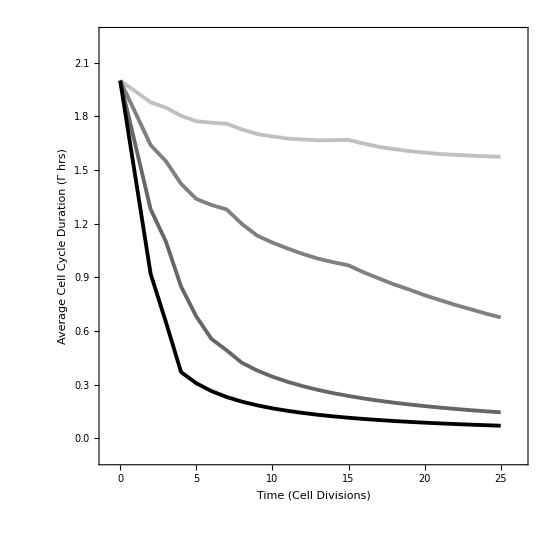

```mathematica
(*
markers = {{-Graphics-, 0.04}, {-Graphics-, 0.04}, {-Graphics-, 0.05}, {-Graphics-, 0.04}};
markers={-Graphics-,-Graphics-,-Graphics-}*)
gnF2=ListPlot[Transpose[{Range[0,25],#}]&/@diversity1,PlotRange->{{-0.85,26.25},{-0.1,2.25}},FrameStyle->Directive[Opacity[1],Black],FrameTicksStyle->Opacity[1],AspectRatio->1,Axes->False,Frame->True,
(*PlotStyle->{Directive[{Lighter[Gray,0.5],Thickness[0.005]}],Directive[{ColorData["ThermometerColors"][0.15],Thickness[0.005]}],Directive[{Brown,Thickness[0.005]}],Directive[{Darker[Pink,0.1],Thickness[0.005]}]}*)PlotStyle->{Directive[{Lighter[Gray,0.5],Thickness[0.005]}],
Directive[{Lighter[Black,0.5],Thickness[0.005]}],
Directive[{Darker[Gray,0.2],Thickness[0.005]}],Directive[{Darker[Black,0.1],Thickness[0.005]}]},BaseStyle->{20},Joined->True,PlotMarkers->None(*{markers,5}*),FrameTicks->{Automatic,{Automatic,Automatic}},FrameLabel->{"Time (Cell Divisions)","Average Cell Cycle Duration (Γ hrs)"},(*PlotLabel->"Same Number of Genes",*)
(*Epilog->{(*Text[Style[dc[[1]]ToString[gNmeMax[[1]] ] ,28],Center,{1.3,-10.1}],Text[Style[dc[[2]]ToString[gNmeMax[[2]] ] ,28],Center,{-1.3,-5.1}],*)
Text[Style["Γ_1 1.00 hr",Lighter[Gray,0.5]],Center,{-3.4,12}],
Text[Style["Γ_2 hrs",ColorData["ThermometerColors"][0.15]],Center,{-0.4,-3}],Text[TableForm[{Style[#,Lighter[Gray,0.5]]&/@{1,2,5},Style[#,ColorData["ThermometerColors"][0.15]]&/@{1,2,5}},TableHeadings->{None,{"L_1","L_G","G"}}],Center,{-0.4,-5}]},*)
(*PlotLegends->(*Placed[*)LineLegend[Style[dc[[#]]ToString[gNmeMax[[#]] ] ,16]&/@Range[1,Length[dc]]](*,{Center,{-0.2,0.2}}*)(*,{Center,Right}]*),*)ImageSize->550,ImagePadding->{{Automatic, 10}, {Automatic, 10}},InterpolationOrder->1]
```

```mathematica
bc=Partition[{{0,0,0,0,4999,0},{0,0,0,4,9994,0},{0,0,0,937,14060,0},{0,0,4,3114,16878,0},{0,0,245,7975,16775,0},{0,0,926,11776,17292,0},{0,0,933,14328,19732,0},{0,0,1000,17458,21534,0},{0,68,3355,20343,21225,0},{0,242,6128,22362,21258,0},{0,248,7065,27155,20521,0},{0,286,8610,30394,20698,0},{0,286,8938,35252,20511,0},{0,292,9768,38900,21026,0},{0,292,9823,42544,22326,0},{0,292,10098,45798,23796,0},{16,1291,14204,45683,23789,0},{70,2762,17332,46028,23790,0},{70,3077,21276,46843,23715,0},{78,3740,24736,47714,23712,0},{78,3844,28060,49469,23528,0},{78,4200,31244,50860,23596,0},{79,4240,33619,53776,23263,0},{80,4412,36170,55986,23328,0},{105,4432,38047,59521,22870,0},{128,4540,40416,61952,22938,0},{0,0,0,0,4999,0},{0,0,0,1134,8864,0},{0,0,759,12812,1426,0},{0,200,6878,11922,996,0},{128,5919,9019,8945,984,0},{2402,10412,7382,8814,984,0},{2402,10753,16220,5582,36,0},{2502,14458,18872,4134,26,0},{11195,11697,17941,4132,26,0},{17116,10798,17918,4132,26,0},{21300,15473,14132,4058,26,0},{27872,14194,13838,4058,26,0},{30359,20631,10251,3720,26,0},{35860,20778,9608,3714,26,0},{37224,25349,10739,1655,18,0},{40272,28654,9462,1578,18,0},{44746,29149,10001,1079,8,0},{49302,29834,9790,1048,8,0},{55247,28863,9982,883,6,0},{60140,29026,9932,876,6,0},{66448,27719,9955,851,6,0},{71494,27682,9946,850,6,0},{78051,26201,9881,838,6,0},{83208,26046,9878,838,6,0},{89374,24995,9762,838,6,0},{94560,24810,9760,838,6,0},{0,0,0,0,4999,0},{0,0,100,9550,348,0},{9,5295,9628,65,0,0},{7768,5698,6488,42,0,0},{15001,3472,6480,42,0,0},{20000,3472,6480,42,0,0},{26463,3452,5050,28,0,0},{31714,3200,5050,28,0,0},{36713,3200,5050,28,0,0},{41712,3200,5050,28,0,0},{46711,3200,5050,28,0,0},{51710,3200,5050,28,0,0},{56709,3200,5050,28,0,0},{61708,3200,5050,28,0,0},{66707,3200,5050,28,0,0},{71706,3200,5050,28,0,0},{76705,3200,5050,28,0,0},{81704,3200,5050,28,0,0},{86703,3200,5050,28,0,0},{91702,3200,5050,28,0,0},{96701,3200,5050,28,0,0},{101700,3200,5050,28,0,0},{106699,3200,5050,28,0,0},{111698,3200,5050,28,0,0},{116697,3200,5050,28,0,0},{121696,3200,5050,28,0,0},{0,0,0,0,4999,0},{0,8,7422,2568,0,0},{12367,2630,0,0,0,0},{18230,1766,0,0,0,0},{23229,1766,0,0,0,0},{28228,1766,0,0,0,0},{33227,1766,0,0,0,0},{38226,1766,0,0,0,0},{43225,1766,0,0,0,0},{48224,1766,0,0,0,0},{53223,1766,0,0,0,0},{58222,1766,0,0,0,0},{63221,1766,0,0,0,0},{68220,1766,0,0,0,0},{73219,1766,0,0,0,0},{78218,1766,0,0,0,0},{83217,1766,0,0,0,0},{88216,1766,0,0,0,0},{93215,1766,0,0,0,0},{98214,1766,0,0,0,0},{103213,1766,0,0,0,0},{108212,1766,0,0,0,0},{113211,1766,0,0,0,0},{118210,1766,0,0,0,0},{123209,1766,0,0,0,0},{123209,1766,0,0,0,0}},UpTo[26]];
```

```mathematica
legen=SwatchLegend[coloB,Reverse[{0,1,1.25,1.5,1.75,2,">2"}](*{"3.0","2.5","2.0","1.5","1.0","0.0"}*),LegendLayout->"Column",LegendMarkerSize->15,LegendLabel->Placed["Cell cycle duration, Γ hrs",Right,Rotate[Style[#,16],-90Degree]&]]
```

```mathematica
pie=Table[PieChart[#,ChartStyle->col[Union[Flatten[Select[(#/(#/. 0->1) *Range[1,6]),#>0&]&/@bc[[i]]]]](*ChartLabels->(If[If[incr1[[1]]==-3,#≠4,#≠3],"",Style[ToString[NumberForm[N[bc[[i,#]]]*100,{3,0}]]<>"%",14]]&/@pos[[i]])*)(*,Frame->True,FrameLabel->{None,"Frequency"},AspectRatio->1,Axes->False,Frame->True,BaseStyle->{16,Black},FrameStyle->Directive[{Black,Thickness[0.005]}],PlotRange->{{0.5,2.5},{0,1}},*)]&/@bc[[i]],{i,Length[bc]}];
```

{1,3,6,9,11,13,16,19,21,23,26}

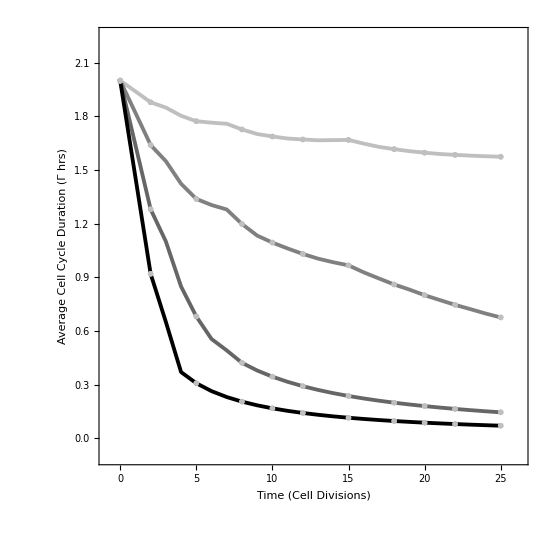

```mathematica
selDiv={1,3,6,9,11,13,16,19,21,23,26}
gnF4=Show[Show[gnF2,PlotStyle->Gray],Table[ListPlot[#[[1]],PlotRange->{{-0.85,26.25},{0,2.5}},FrameStyle->Directive[Opacity[1],Black],FrameTicksStyle->Opacity[1],AspectRatio->1,Axes->False,Frame->True,
PlotStyle->{Directive[{Lighter[Gray,0.5],Thickness[0.005]}],Directive[{ColorData["ThermometerColors"][0.15],Thickness[0.005]}],Directive[{Brown,Thickness[0.005]}],Directive[{Darker[Pink,0.1],Thickness[0.005]}]},BaseStyle->{20},Joined->True,PlotMarkers->Show[#[[2]],ImageSize->31],FrameTicks->{Automatic,{Automatic,Automatic}},FrameLabel->{"Time (Cell Divisions)","Average Cell Cycle Duration (Γ hrs)"},(*PlotLabel->"Same Number of Genes",*)
(*Epilog->{(*Text[Style[dc[[1]]ToString[gNmeMax[[1]] ] ,28],Center,{1.3,-10.1}],Text[Style[dc[[2]]ToString[gNmeMax[[2]] ] ,28],Center,{-1.3,-5.1}],*)
Text[Style["Γ_1 1.00 hr",Lighter[Gray,0.5]],Center,{-3.4,12}],
Text[Style["Γ_2 hrs",ColorData["ThermometerColors"][0.15]],Center,{-0.4,-3}],Text[TableForm[{Style[#,Lighter[Gray,0.5]]&/@{1,2,5},Style[#,ColorData["ThermometerColors"][0.15]]&/@{1,2,5}},TableHeadings->{None,{"L_1","L_G","G"}}],Center,{-0.4,-5}]},*)
(*PlotLegends->(*Placed[*)LineLegend[Style[dc[[#]]ToString[gNmeMax[[#]] ] ,16]&/@Range[1,Length[dc]]](*,{Center,{-0.2,0.2}}*)(*,{Center,Right}]*),*)ImageSize->540,ImagePadding->{{Automatic, 10}, {Automatic, 10}}]&/@Transpose[{Partition[Transpose[{selDiv-1,diversity1[[i,selDiv]]}],1],pie[[i,selDiv]]}],{i,1,4}]]
```

```mathematica
Export["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/FigsourceFiles2019/output/6-Figure6_decreasing.nb",gnF4(*GraphicsColumn[{gfAB,gfD},Spacings->-50]*)]
```

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/FigsourceFiles2019/output/6-Figure6_decreasing.nb

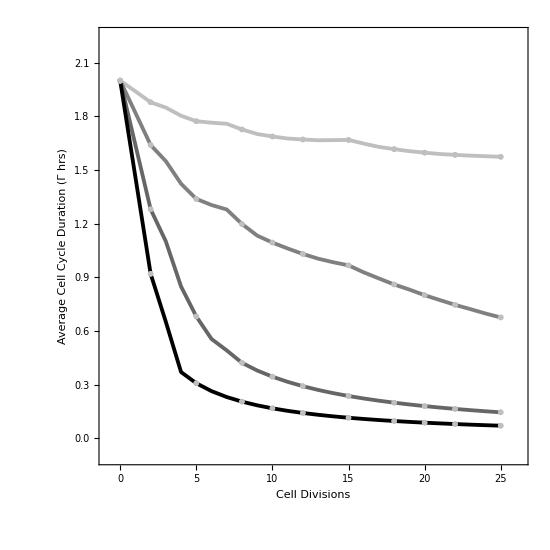
-Graphics-B

```mathematica
gfB=Panel[gnF4,Style["B",30,Black,Bold],Appearance->"Frameless",Background->White]
```

```mathematica
Export["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/6Figure6_decreasing_B.nb",gfB(*GraphicsColumn[{gfAB,gfD},Spacings->-50]*)]
Export["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/6Figure6_decreasing_B.pdf",gfB(*GraphicsColumn[{gfAB,gfD},Spacings->-50]*)]
```

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/6Figure6_decreasing_B.nb

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/6Figure6_decreasing_B.pdf